```mathematica
Simplify[(2/L)*(Integrate[(x^2)*(Sin((Pi*x)/L))*(Sin((2*Pi*x)/L)),{x, 0, L}])]
```

```mathematica
4/5 L^2 π^2 Sin^2
(*Define and compute the integral*)
integral=(2/L)*Integrate[x^2*Sin[Pi*x/L]*Sin[2*Pi*x/L],{x,0,L},Assumptions->L>0]

(*Simplify the result*)
Simplify[integral,Assumptions->L>0]
```

4/5 L^2 π^2 Sin^2

-(16 L^2)/(9 π^2)

```mathematica
-(16 L^2)/(9 π^2)
(*σ_H·σ_t/ℏ as a function of θ*)f[θ_]:=(9π^2/32)*Sqrt[1/12-5/(16π^2)-8Cos[θ]/(9π^2)-256Cos[θ]^2/(81π^4)]/Abs[Sin[θ]]

(*Minimum value*)
NMinimize[{f[θ],0.01<θ<π-0.01},θ]

(*Plot*)
Plot[f[θ],{θ,0.01,π-0.01}]
```

-(16 L^2)/(9 π^2)

NMinimize::nrnum: The function value 0.+4.79324 ⅈ is not a real number at {θ} = {0.152756}.

NMinimize[{(9 π^2 √(1/12-5/(16 π^2)-(8 Cos[θ])/(9 π^2)-(256 Cos[θ]^2)/(81 π^4)))/(32 Abs[Sin[θ]]),0.01<θ<3.13159},θ]

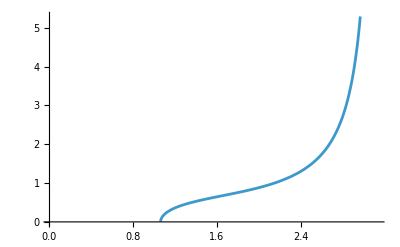
```mathematica
-Graphics-
f[θ_]:=(9π^2/32)*Sqrt[1/12-5/(16π^2)-8Cos[θ]/(9π^2)-256Cos[θ]^2/(81π^4)]/Abs[Sin[θ]]

(*Find minimum numerically*)
NMinimize[{f[θ],0.1<θ<π/2},θ]

(*Or just evaluate at a grid of points to find the minimum*)
Table[{θ,f[θ]},{θ,0.1,π/2,0.05}]//N
```

-Graphics-

NMinimize::nrnum: The function value 0.+4.36962 ⅈ is not a real number at {θ} = {0.167262}.

NMinimize[{(9 π^2 √(1/12-5/(16 π^2)-(8 Cos[θ])/(9 π^2)-(256 Cos[θ]^2)/(81 π^4)))/(32 Abs[Sin[θ]]),0.1<θ<π/2},θ]

```mathematica
{{0.1,0.+7.359818673904965 ⅈ},{0.15000000000000002,0.+4.8828989684347155 ⅈ},{0.2,0.+3.637107791384062 ⅈ},{0.25,0.+2.8835702416868614 ⅈ},{0.30000000000000004,0.+2.375937522968582 ⅈ},{0.35,0.+2.008575132849208 ⅈ},{0.4,0.+1.7286073482477486 ⅈ},{0.45000000000000007,0.+1.5065956003908356 ⅈ},{0.5,0.+1.3248058342998477 ⅈ},{0.55,0.+1.1718701457352045 ⅈ},{0.6,0.+1.0401101018868546 ⅈ},{0.65,0.+0.9240844019406539 ⅈ},{0.7000000000000001,0.+0.8197417564724085 ⅈ},{0.75,0.+0.7238840148128762 ⅈ},{0.8,0.+0.6337791997142621 ⅈ},{0.85,0.+0.5468088931310405 ⅈ},{0.9,0.+0.4600004118671243 ⅈ},{0.9500000000000001,0.+0.3690605022497017 ⅈ},{1.,0.+0.26519093564541973 ⅈ},{1.05,0.+0.10970220331772791 ⅈ},{1.1,0.2004667275087757},{1.1500000000000001,0.29589370453202873},{1.2000000000000002,0.3620127224721786},{1.2500000000000002,0.41413457269328546},{1.3000000000000003,0.45783083590834234},{1.35,0.49594030216573237},{1.4000000000000001,0.530169677359042},{1.4500000000000002,0.5616570765813422},{1.5000000000000002,0.5912202416764539},{1.5500000000000003,0.6194828266313009}}
f[θ_]:=(9π^2/32)*Sqrt[1/12-5/(16π^2)-8Cos[θ]/(9π^2)-256Cos[θ]^2/(81π^4)]/Abs[Sin[θ]]

NMinimize[{f[θ],0.1<θ<π-0.1},{θ}]//N
```

{{0.1,0.+7.35982 ⅈ},{0.15,0.+4.8829 ⅈ},{0.2,0.+3.63711 ⅈ},{0.25,0.+2.88357 ⅈ},{0.3,0.+2.37594 ⅈ},{0.35,0.+2.00858 ⅈ},{0.4,0.+1.72861 ⅈ},{0.45,0.+1.5066 ⅈ},{0.5,0.+1.32481 ⅈ},{0.55,0.+1.17187 ⅈ},{0.6,0.+1.04011 ⅈ},{0.65,0.+0.924084 ⅈ},{0.7,0.+0.819742 ⅈ},{0.75,0.+0.723884 ⅈ},{0.8,0.+0.633779 ⅈ},{0.85,0.+0.546809 ⅈ},{0.9,0.+0.46 ⅈ},{0.95,0.+0.369061 ⅈ},{1.,0.+0.265191 ⅈ},{1.05,0.+0.109702 ⅈ},{1.1,0.200467},{1.15,0.295894},{1.2,0.362013},{1.25,0.414135},{1.3,0.457831},{1.35,0.49594},{1.4,0.53017},{1.45,0.561657},{1.5,0.59122},{1.55,0.619483}}

NMinimize::nrnum: The function value 0.+3.08317 ⅈ is not a real number at {θ} = {0.234524}.

General::stop: Further output of NMinimize::nrnum will be suppressed during this calculation.

NMinimize[{(2.77583 √(0.0516705-0.0900633 Cos[θ]-0.0324456 Cos[θ]^2))/Abs[Sin[θ]],0.1<θ<3.04159},{θ}]